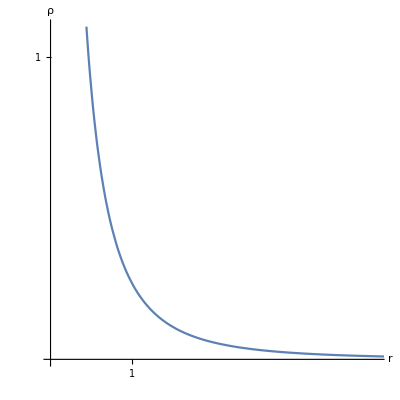

```mathematica
font={LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 32}};
rho[r_]=1/(r(1+r)^2);
Plot[rho[r],{r,0,10},Ticks->{{1},{1}},AxesLabel->{"r","ρ"},Evaluate@font,PlotRange->{{0,4},{0,1.1}},AspectRatio->1,TicksStyle->Directive["Label", 1]]
```

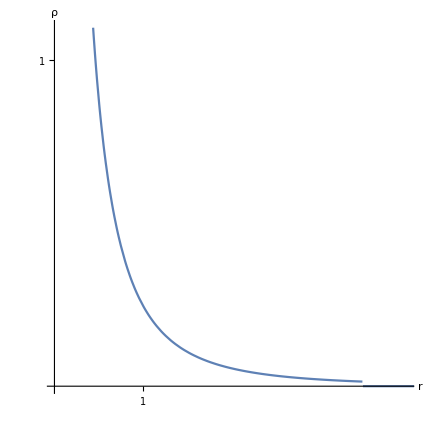

```mathematica
Plot[rho[r]HeavisideTheta[3.5-r],{r,0,10},Ticks->{{1},{1}},AxesLabel->{"r","ρ"},Evaluate@font,PlotRange->{{0,4},{0,1.1}},AspectRatio->1,TicksStyle->Directive["Label", 1]]
```